# Project: nrmma

Wolfram Workbench 18-Jan-2012.

This notebook is created to test the project.

```mathematica
<<nrmma`
```

Loading nrmma

Loading h5mma

```mathematica
run="bbh-git";
```

```mathematica
ReadIHSpin[run,0]
```

Throw::nocatch: Uncaught Throw["Cannot find file ihspin_hn_0.asc in run bbh-git"] returned to top level.

Hold[Throw[Cannot find file ihspin_hn_0.asc in run bbh-git]]

```mathematica
ReadIHSpinX[run,0]
```

Throw::nocatch: Uncaught Throw["Cannot find file ihspin_hn_0.asc in run bbh-git"] returned to top level.

Hold[Throw[Cannot find file ihspin_hn_0.asc in run bbh-git]]

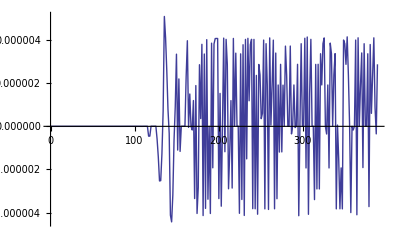

```mathematica
ListLinePlot[ReadIsolatedHorizonSpin[run,0,1]]
```

```mathematica
Short[ToList@ReadIsolatedHorizonDimensionlessSpin[run,0],10]
```

{{0.,{5.34247×10^-31,1.07544×10^-33,5.66521×10^-17}},{1.44,{1.76811×10^-20,1.44231×10^-19,2.73097×10^-10}},{2.88,{1.34962×10^-20,7.49029×10^-20,5.44366×10^-10}},«265»,{385.92,{8.46458×10^-13,7.27231×10^-13,0.428353}},{387.36,{1.35723×10^-13,5.79282×10^-14,0.428382}},{388.8,{9.14101×10^-12,2.68446×10^-11,0.428355}}}

```mathematica
Short[ToList@ReadIsolatedHorizonSpinPhase[run,0],10]
```

{{0,0.0448363},{1.44,1.90758},{2.88,4.31096},{4.32,3.22765},{5.76,0.114655},{7.2,2.77244},{8.64,3.01491},{10.08,3.72431},{11.52,3.43682},{12.96,4.49482},{14.4,7.26529},«250»,{375.84,36.778},{377.28,38.7706},{378.72,35.8335},{380.16,38.8027},{381.6,38.348},{383.04,38.7087},{384.48,38.8831},{385.92,38.4466},{387.36,41.4194},{388.8,38.7417}}

```mathematica
Short[ToList[ReadAHMass[run,1]]]
```

{{0.,0.499999},{1.44,0.499997},«265»,{388.8,0.883897}}

```mathematica
Short[ToList[ReadAHRadius[run,1]]]
```

{{0.,0.227072},{1.44,0.376954},«265»,{388.8,0.736294}}

```mathematica
Short[ToList[ReadAHMinRadius[run,1]]]
```

{{0.,0.220053},{1.44,0.35964},«265»,{388.8,0.677842}}

```mathematica
Short[ToList[ReadAHMaxRadius[run,1]]]
```

{{0.,0.234383},{1.44,0.393205},«265»,{388.8,0.763835}}

```mathematica
Short[ToList[ReadAHCentroid[run,1]]]
```

{{0.,{2.99999,-0.002378,0.}},«266»,{388.8,{-8.×10^-6,-0.000052,-0.000013}}}

```mathematica
Short[ToList[ReadAHCentroidCoord[run,1,1]]]
```

{{0.,2.99999},{1.44,2.99399},«264»,{387.36,-8.×10^-6},{388.8,-8.×10^-6}}

```mathematica
Short[ToList[ReadAHColumn[run,1,12]]]
```

{{0.,0.0172067},{1.44,0.0472235},«265»,{388.8,0.195812}}

```mathematica
Short[ToList@ReadAHColumns[run,1,{5,6,7}]]
```

{{0.,{0.,0.220053,0.234383}},«266»,{388.8,{-0.000013,«12»,«13»}}}

```mathematica
Short@ToList@ReadAHQuadrupoleXX[run,1]
```

{{0.,0.0171835},{1.44,0.0474235},«265»,{388.8,0.195913}}

```mathematica
Short@ToList@ChristodoulouMass[run,1,0]
```

{{0.,0.499999},«269»,{388.8,0.951511}}

```mathematica
Short@ToList@ReadAHSeparation[run]
```

{{0.,5.99998},{1.44,5.99203},«265»,{388.8,0.}}

```mathematica
Short@ToList@ReadAHPhase[run]
```

{{0.,-0.000792669},«266»,{388.8,4 π}}

```mathematica
InitialSpin[run,0]
```

Throw::nocatch: Uncaught Throw["Cannot find file ihspin_hn_0.asc in run bbh-git"] returned to top level.

Hold[Throw[Cannot find file ihspin_hn_0.asc in run bbh-git]]

```mathematica
SpinAngle[run,0]
```

Throw::nocatch: Uncaught Throw["Cannot find file ihspin_hn_0.asc in run bbh-git"] returned to top level.

Hold[Throw[Cannot find file ihspin_hn_0.asc in run bbh-git]]

```mathematica
InitialSpinAngle[run,0]
```

Throw::nocatch: Uncaught Throw["Cannot find file ihspin_hn_0.asc in run bbh-git"] returned to top level.

Hold[Throw[Cannot find file ihspin_hn_0.asc in run bbh-git]]